```mathematica
(* 
Terahertz wave propagation in uniform nanorods:A nonlocal continuum
mechanics formulation including the effect of lateral inertia
S.Narendar
 *)
```

```mathematica
Clear[Evaluate[Context[]<>"*"]];
Needs["PlotLegends`"]

u[x_,t_]:= Exp[-I(k x - ω t)];
ωCl[k_]=Solve[D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]];
ωStrainG[k_]=Solve[α^2 D[u[x,t],{x,4}]+D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]]//FullSimplify;
ωStrain4G[k_]=Solve[ α^4 D[u[x,t],{x,6}]+ α^2 D[u[x,t],{x,4}]+D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]]//FullSimplify;
ωStressG[k_]= Solve[D[u[x,t],{x,2}]+(ρ/Ev)α^2 D[D[u[x,t],{t,2}],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]];
ωBK[k_]=(2/0.142)Sqrt[Ev/ρ]Sin[k * 0.142/2];
ωStressGIn[k_]=Solve[Ev D[u[x,t],{x,2}]== ρ D[u[x,t],{t,2}] - ρ ν^2ζ^2 D[D[u[x,t],{t,2}],{x,2}]-α^2 ρ D[D[u[x,t],{t,2}],{x,2}]+α^2 ρ ν^2ζ^2D[D[u[x,t],{t,2}],{x,4}],ω][[2,1,2]];
```

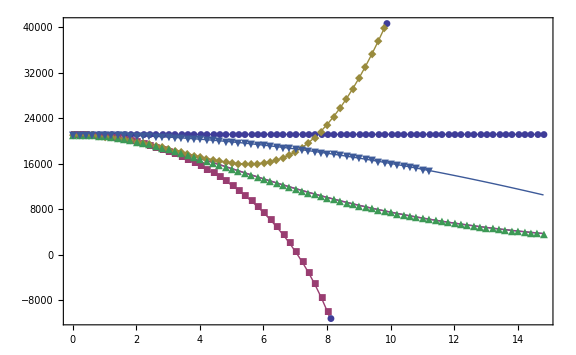

```mathematica
Ev = 1.03 * 10^12;
ρ = 2300;
α= 0.1 ;
r = 3.5 * 10^(-9);
t = 0.35 * 10^(-9);
A = 2 * Pi * r * t;
a=0.142;
ν = 0.280;
ζ = 0.238095 10^(-9);

(* Phase Velocity *)
VgCl[x_]=D[ωCl[x],x];
VgStrainG[x_]=D[ωStrainG[x],x];
VgStrain4G[x_]=D[ωStrain4G[x],x];
VgStressG[x_]=D[ωStressG[x],x];
VgBK[x_]=D[ωBK[x],x];
VgStressGIn[x_]=D[ωStressGIn[x],x];
(*VgStrainG[k]/.{k->Range[0.1,15,15/10]}*)
(*Map[VgStrainG,Range[10]]*)
(*Flatten[{Range[0.1,15,15/100],VgStrainG[k]/.{k->Range[0.1,15,15/100]}},{{2},{1}}];*)
(*
ListPlot[
Flatten[{Range[0.1,15,15/20],ωStrainG[k]/.{k->Range[0.1,15,15/20]}},{{2},{1}}],
LegendShadow->None,
LegendPosition->{-0.5,-1.65},
LegendSize->{1.5,1},
ImageSize->Large
]*)
points1=Table[{x,VgCl[x]},{x,Range[0.01,15,0.2]}];
points2=Table[{x,VgStrainG[x]},{x,Range[0.01,15,0.2]}];
points3=Table[{x,VgStrain4G[x]//Evaluate},{x,Range[0.01,15,0.2]}];
points4=Table[{x,VgStressG[x]//Evaluate},{x,Range[0.01,15,0.2]}];
points5=Table[{x,VgBK[x]//Evaluate},{x,Range[0.01,15,0.2]}];
points6=Table[{x,VgStressGIn[x]//Evaluate},{x,Range[0.01,15,0.2]}];


ListLinePlot[{points1,points2,points3,points4,points5,points6},
PlotMarkers->Automatic,ImageSize->Large,
PlotLegend->{"Local Model","NL  II order strain gradient",
"NL 4th order strain gradient",
"NL stress gradient model","Born-Karman model","NL Stress Gr with Inertia"
},
LegendShadow->None,
LegendPosition->{-0.7,0.25},
LegendSize->{0.9,0.4},
ImageSize->Large,
Frame->True,
FrameLabel->{"Wave number (1/nm)","Group velocity (m/s)"}
]
(*Plot[{VgStressG[x],VgStrainG[x],VgStress4G[x]},{x,0,15},AxesOrigin->{0,0}]*)
```

```mathematica
￿
```

￿

```mathematica
(*Flatten[{(ωCl[k]/(1000 4 Pi))/.{k->Range[0,15]},Range[0,15]},{{2},{1}}]*)
(ωCl[k]/(1000 4 Pi))/.{k->Range[0,15]}
```

{0,1.68401,3.36802,5.05203,6.73604,8.42005,10.1041,11.7881,13.4721,15.1561,16.8401,18.5241,20.2081,21.8921,23.5761,25.2602}